# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
ParallelEvaluate[ClearAll["Global`*"]];
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
CloseKernels[];
LaunchKernels[];
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
choiceslist={"Tabulated Nevents+sensitivity","Sensitivity only (tabulated Nevents must be produced before)","Acceptance"};
taglist["Acceptance"]="Acceptance";
taglist["Tabulated Nevents+sensitivity"]="Number-of-events+sensitivity";
taglist["Sensitivity only (tabulated Nevents must be produced before)"]="Sensitivity";
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulated number of events has been already produced)?"];
tagselected=taglist[computationchoice]
BlockEvaluation[tagselected]
```

Number-of-events+sensitivity

# Preliminary definitions (launch first)

## Various directories

```mathematica
LLPdirName="HNL";
(*Set the directory for the search where tabulated acceptances are located*)
directory["Acceptances"]=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
(*Set the directory for the search where tabulated angle-energy distributions are located*)
directory["Distribution"]=FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra",LLPdirName}]; 
(*The directory storing production weights of the given LLP*)
directory["Production weights"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"Production probabilities"}]; 
(*Directory to which various auxillary datasets will be stored*)
directory["Auxiliary"]=FileNameJoin[{NotebookDirectory[],"Auxiliary data",LLPdirName}]; 
If[!DirectoryQ[directory["Auxiliary"]],CreateDirectory[directory["Auxiliary"]]];
(*Directory containing decay widths of the LLPs*)
directory["Decays"]=FileNameJoin[{NotebookDirectory[],"phenomenology",LLPdirName,"decay widths"}];
```

## Parameters and various functions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*Masses of various SM particles*)
{mSM["e"],mSM["mu"],mSM["tau"]}={0.5*10^-3,0.105,1.77};
{mSM["W"],mSM["Z"]} = {80.369,91.1876};
{mSM["e"],mSM["mu"],mSM["PiCharged"]}={0.5*10^-3,0.105,0.139};
```

## LLP phenomenology: prodution probabilities, decay widths

## Scanning for tabulated distributions

```mathematica
(*Define the file pattern*)
pattern="DoubleDistr_*_*_*.m";
(*Search for files matching the pattern in the directory and its subdirectories*)
matchingFiles=FileNames[pattern,{directory["Distribution"]},Infinity];
(*List of LLPs, production modes, and facilities for which the tabulated distributions have been computed at the previous stage of using SensCalc*)
ExtractedProductionParameters=Function[filename,parts=StringSplit[FileNameTake[filename],"_"];
{parts[[2]],parts[[3]],StringDrop[parts[[4]],-2]} ];
(*Apply the function to each file in the list*)
DistrCombinations=(ExtractedProductionParameters/@matchingFiles)//Sort;
HNLsList={"HNL-mixing-e","HNL-mixing-mu","HNL-mixing-tau"};
(DistrCombinations[[All,1]]//DeleteDuplicates//Sort)==HNLsList
```

True

## Production weights

```mathematica
(*For mesons: ∑_meson Subscript[f, q->meson]*Br(meson->N) at U^2 = 1*)
(*For X = W/Z: Br(X->N) at U^2 = 1*)
ProductionWeightsTemp[mN_]=Import[FileNameJoin[{directory["Production weights"],"ProductionWeightsHNL.m"}],"MX"];
Do[
Module[{hnl,prod,facility},
{hnl,prod,facility}=ProductionWeightsTemp[mLLP][[i]][[#]]&/@{1,2,3};
ProdMotherToLLP[mLLP_,U2_,hnl,prod,facility]=U2*ProductionWeightsTemp[mLLP][[i]][[4]];
]
,{i,1,Length[ProductionWeightsTemp[mLLP]],1}]
WeightsCombinations=ProductionWeightsTemp[mLLP][[All,{1,2,3}]]//Sort;
WeightsCombinations=Cases[WeightsCombinations,_?(MemberQ[DistrCombinations,#]&)];
IfCondDistrToWeights=DistrCombinations==WeightsCombinations;
If[!IfCondDistrToWeights,infoDialog["You have not provided the production probabilities PmotherToLLP to all the generated tabulated distributions! Please do this first to avoid problems"];]
```

## Decay width

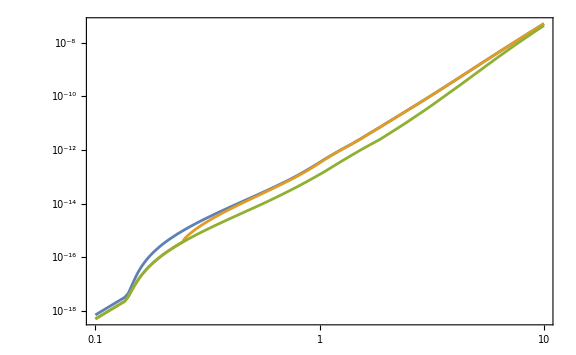

```mathematica
Γtable=Import[FileNameJoin[{directory["Decays"],"HNLdecayWidth.dat"}],"Table"];
{DecayWidth[mLLP_,U2_,HNLsList[[1]]],DecayWidth[mLLP_,U2_,HNLsList[[2]]],DecayWidth[mLLP_,U2_,HNLsList[[3]]]}=U2(10^Interpolation[{#[[1]],Log10[#[[2]]+10^-99]}&/@Γtable[[All,{1,#}]],InterpolationOrder->1][mLLP])&/@{2,3,4};
LogLogPlot[Evaluate[DecayWidth[mLLP,1,"HNL-mixing-"<>#]&/@{"e","mu","tau"}],{mLLP,0.1,10},Frame->True,ImageSize->Large]
```

## Loading necessary routines

```mathematica
If[Length[inecessary]==0,
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/generic.nb"}]];
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"codes/for-sensitivities.nb"}]];
inecessary={1,2,3};
]
```

# Specifying the experiment and HNL

## HNL

```mathematica
ListHNLtype={"Dirac","Majorana"};
HNLtype=dropdownDialog[ListHNLtype,"Select the HNL type:"];
Print["HNL type:"]
HNLtype
{MixingPatterne,MixingPatternμ,MixingPatternτ}=DialogInput[{pattern={1.,0.,0.}},Column[{"Enter the mixing pattern (U^2)_e:(U^2)_μ:(U^2)_τ = U^2(x_e:x_μ:x_τ) (where Σ_ix_i = 1) in the form {xe,xμ,xτ}:",InputField[Dynamic[pattern],Expression],Button["Proceed",DialogReturn[pattern],ImageSize->Automatic]}]]//N;
Print["Mixing pattern:"]
MixingPattern=(MixingPatterne+MixingPatternμ+MixingPatternτ)^-1{MixingPatterne,MixingPatternμ,MixingPatternτ}//N
ΓLLP[mLLP_,U2_]=If[HNLtype=="Dirac",1/2,1](DecayWidth[mLLP,U2,#]&/@HNLsList).MixingPattern//Chop
cτLLP[mLLP_,U2_]=chbar/ΓLLP[mLLP,U2];
ldecayLLP[mLLP_,U2_,EN_]=(√(EN^2-mLLP^2))/mLLP*cτLLP[mLLP,U2];
```

HNL type:

Dirac

Set::shape: Lists {MixingPatterne,MixingPatternμ,MixingPatternτ} and {0.34.,0.33,0.33} are not the same shape.

Mixing pattern:

{MixingPatterne/(MixingPatterne+MixingPatternμ+MixingPatternτ),MixingPatternμ/(MixingPatterne+MixingPatternμ+MixingPatternτ),MixingPatternτ/(MixingPatterne+MixingPatternμ+MixingPatternτ)}

1/2 ((10^(InterpolatingFunction[…](mLLP)) MixingPatterne U2)/(MixingPatterne+MixingPatternμ+MixingPatternτ)+(10^(InterpolatingFunction[…](mLLP)) MixingPatternμ U2)/(MixingPatterne+MixingPatternμ+MixingPatternτ)+(10^(InterpolatingFunction[…](mLLP)) MixingPatternτ U2)/(MixingPatterne+MixingPatternμ+MixingPatternτ))

## Experiments

```mathematica
ExperimentDirectoriesList=Select[FileNames["*",directory["Acceptances"],1],DirectoryQ];
(*List of the experiments for which any tabulated acceptance has been produced*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
IfHNL[exp_]:=Module[{},
expf=FileNameJoin[{directory["Acceptances"],exp}];
tabEx=FileExistsQ[FileNameJoin[{expf,"Acceptance_"<>exp<>"_for_"<>#<>".m"}]]&/@HNLsList;
!MemberQ[tabEx,False]
]
ExperimentsList=Select[ExperimentsListTemp,IfHNL[#]&]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiments:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{"Select the experiments for which the number of events will be computed:"}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
SelectedExperimentList=If[Length[ExperimentsList]≠0,selectionDialog[ExperimentsList,"Select the experiments:"]]
icounter=1;
```

{SHiP-ECN4}

Selected experiments:

{SHiP-ECN4}

## Running block for next sections

```mathematica
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
If[tagselected=="Number-of-events+sensitivity",
Do[
BlockEvaluation["Number-of-events-computation+sensitivity"];
,{icounter,1,Length[SelectedExperimentList],1}],
If[tagselected=="Acceptance",
Do[
BlockEvaluation["Acceptance-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
]
```

# Number of events

## Particular experiment

```mathematica
SelectedExperiment=SelectedExperimentList[[icounter++]];
```

## Cross-sections, acceptances

## Importing data for separate mixings

{0.852867,Null}

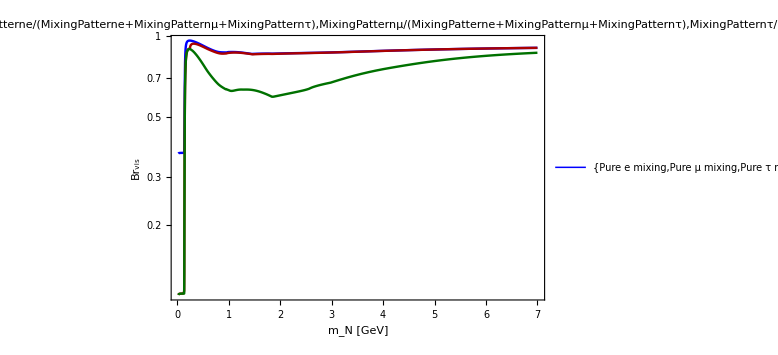

Search for Dirac HNLs with the mixing pattern {U_e^2,U_μ^2,U_τ^2} = U^2{MixingPatterne/(MixingPatterne+MixingPatternμ+MixingPatternτ),MixingPatternμ/(MixingPatterne+MixingPatternμ+MixingPatternτ),MixingPatternτ/(MixingPatterne+MixingPatternμ+MixingPatternτ)} at SHiP-ECN4 located at SPS. N_collisions = 6.×10^20

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.00001 | 0.0602815 | 0.00001 | 0.0602815 | 50. | 100.

```mathematica
Do[
ExperimentData[HNLsList[[i]]]=Import[FileNameJoin[{FileNameJoin[{directory["Acceptances"],SelectedExperiment,"Acceptance_"<>SelectedExperiment<>"_for_"<>HNLsList[[i]]<>".m"}]}],"MX"];
AcceptanceData[HNLsList[[i]]]=ExperimentData[HNLsList[[i]]][[3]];
BrVisMixing[mLLP_,HNLsList[[i]]]=ExperimentData[HNLsList[[i]]][[5]];
,{i,1,Length[HNLsList],1}]//AbsoluteTiming
{AzimuthalAcceptanceInt[θLLP_,zLLP_],θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp,zminθ[θLLP_],zmaxθ[θLLP_]}=BlockϵAzimuthal[AcceptanceData[HNLsList[[1]]]];
brtemp[mLLP_]=BrVisMixing[mLLP,HNLsList[[1]]];
(*Branching ratio of visible HNL decays averaged over mixings*)
BrVis[mLLP_]=(BrVisMixing[mLLP,HNLsList[[#]]]&/@{1,2,3}.MixingPattern)/(MixingPattern//Total)//Chop;
mlistBr=Join[Table[m,{m,0.02,5.1,0.001}],Table[m,{m,5.12,30,0.01}]];
LogPlot[Evaluate[{BrVisMixing[mLLP,HNLsList[[1]]],BrVisMixing[mLLP,HNLsList[[2]]],BrVisMixing[mLLP,HNLsList[[3]]],BrVis[mLLP]}],{mLLP,Min[mlistBr],7},FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{{0.02,7},All},Frame->True,ImageSize->Large,FrameLabel->{"m_N [GeV]","Br_vis"},PlotLabel-> Style[Row[{"For ",SelectedExperiment,". U_e^2:U_μ^2:U_τ^2 = ",MixingPattern}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"Pure e mixing","Pure μ mixing","Pure τ mixing","Averaged"}},{0.75,0.2}]]
{xxx,yyy,zzz,InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,ϵvals,ϵazvals,mminϵ,mmaxϵ}=BlockϵDecay[AcceptanceData[HNLsList[[1]]],zminExp,brtemp];
FacilityGivenExperiment=ExperimentData[HNLsList[[1]]][[1]];
CrossSectionData=ExperimentData[HNLsList[[1]]][[4]]//Transpose;
NpotGivenExperiment=Select[CrossSectionData,#[[1]]=="Npot"&][[1]][[2]];
(*Amounts (per PoT) of c or c̄, b or b̄, and W^+ or W^- at the given experiment (Subscript[P, c or c̄] = Subscript[P, c]+Subscript[P, c̄] = 2*Subscript[P, c c̄], etc.)*)
{ProbMother["D"],ProbMother["B"],ProbMother["W"]}={Select[CrossSectionData,#[[1]]=="Pc"&][[1]][[2]],Select[CrossSectionData,#[[1]]=="Pb"&][[1]][[2]],Select[CrossSectionData,#[[1]]=="PW"&][[1]][[2]]};
If[FacilityGivenExperiment=="SPS",
ProbMother["K"]=0.36];
If[FacilityGivenExperiment=="ESS",
ProbMother["PiCharged"]=Select[CrossSectionData,#[[1]]=="PPiCharged"&][[1]][[2]];
ProbMother["mu"]=Select[CrossSectionData,#[[1]]=="Pmu"&][[1]][[2]];
];
(*infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]*)
Row[{"Search for ",HNLtype," HNLs with the mixing pattern {U_e^2,U_μ^2,U_τ^2} = U^2",MixingPattern," at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

## Gluing the data for separate mixings to the given mixing pattern

```mathematica
(*Computing weights for decays via different mixing. The weights are Subscript[Br, vis,x]*Subscript[U^2, x]/U^2/Subscript[Σ, x] Subscript[Br, vis,x]*Subscript[U^2, x]/U^2*)
WeightϵDecayMixing=1/BrVis[#]{BrVisMixing[#,HNLsList[[1]]]*MixingPattern[[1]],BrVisMixing[#,HNLsList[[2]]]*MixingPattern[[2]],BrVisMixing[#,HNLsList[[3]]]*MixingPattern[[3]]}&/@(10^InGridmϵ);
(*The averaged decay acceptance: the weights for the given mass and flavor are contracted with the lists of the decay acceptances for the same mass and flavor, and then there is a summation over flavors*)
FullAcceptanceData0=Join[AcceptanceData[HNLsList[[1]]][[All,Range[1,5]]],(List/@Flatten[WeightϵDecayMixing[[All,#]]* Partition[AcceptanceData[HNLsList[[#]]][[All,-1]],Length[AcceptanceData[HNLsList[[#]]]]/Length[InGridmϵ]]]&/@{1,2,3})//Total,2];//AbsoluteTiming
{FullAcceptanceData,DecayAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],FullAcceptanceInt[mLLP_,θLLP_,ELLP_,zLLP_],InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,ϵvals,ϵazvals,mminϵ,mmaxϵ}=BlockϵDecay[FullAcceptanceData0,zminExp,BrVis];
```

{16.5486,Null}

CompiledFunction::cfta: Argument {<<5571393536 bytes>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

General::stop: Further output of CompiledFunction::cfta will be suppressed during this calculation.

## Angle-energy distributions for the given experiment

## Importing for separate mixings

```mathematica
ProductionPatternSelected=Select[DistrCombinations,#[[3]]==FacilityGivenExperiment&];
Print["Production list:"]
ProductionList=ProductionPatternSelected[[All,2]]//DeleteDuplicates;
If[MixingPattern=={0.,0.,1.},ProductionList=Select[ProductionList,#!="K"&]]
Do[
Module[{hnl,prod},
{hnl,prod}=ProductionPatternSelected[[i]][[#]]&/@{1,2};
(*Importing the data with distribution*)
DistrDataImportTemp[hnl,prod]=Import[FileNameJoin[{directory["Distribution"],"DoubleDistr_"<>hnl<>"_"<>prod<>"_"<>FacilityGivenExperiment<>".m"}],"MX"];
ProbLLP[mLLP_,U2_,hnl,prod]=ProbMother[prod]*ProdMotherToLLP[mLLP,U2,hnl,prod,FacilityGivenExperiment];
]
,{i,1,Length[ProductionPatternSelected],1}]
prodsnoτ={"K","PiCharged","mu"};
Do[
If[MemberQ[prodsnoτ,prod],
DistrDataImportTemp[HNLsList[[3]],prod]={#[[1]],#[[2]],#[[3]],0.}&/@DistrDataImportTemp[HNLsList[[1]],prod];
ProbLLP[mLLP_,U2_,HNLsList[[3]],prod]=0.;
]
,{prod,ProductionList}]
```

Production list:

If[{MixingPatterne/(MixingPatterne+MixingPatternμ+MixingPatternτ),MixingPatternμ/(MixingPatterne+MixingPatternμ+MixingPatternτ),MixingPatternτ/(MixingPatterne+MixingPatternμ+MixingPatternτ)}=={0.,0.,1.},ProductionList=Select[ProductionList,#1≠K&]]

## Gluing

```mathematica
Do[ProbLLP[mLLP_,U2_,prod]=Sum[ProbLLP[mLLP,U2,HNLsList[[i]],prod]*MixingPattern[[i]],{i,1,3,1}]//Chop,{prod,ProductionList}];
(*Code supplementing the data for the distribution up to the given mass with zeros*)
DataSupplementedBlock[data_,mmax_]:=Block[{},
mdatamax=Max[data[[All,1]]];
dataθEgrid=SortBy[DeleteDuplicatesBy[data,{#[[2]],#[[3]]}&][[All,{2,3}]],{#[[1]],#[[2]]}&]//N;
Join[data,Flatten[Table[{mLLP,dataθEgrid[[i]][[1]],dataθEgrid[[i]][[2]],0},{mLLP,1.001mdatamax,mmax,(mmax-1.001mdatamax)/3},{i,1,Length[dataθEgrid],1}],{1,2}]]
]
DataLogarithmiedComp1=Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"MVM",RuntimeOptions->"Speed"];
(*The block that glues the distributions according to the mixing pattern*)
BlockDistrGluing[ProdChannel_]:=Block[{},
(*Angle-energy distribution data corresponding to the given production channel*)
DataList=DistrDataImportTemp[#,ProdChannel]&/@HNLsList;
(*List of the production probabilities per mixing for the given production channel: Subscript[P, prod](m,Subscript[U, i]^2/U^2)*)
χlist[mLLP_]=ProbLLP[mLLP,MixingPattern[[#]],HNLsList[[#]],ProdChannel]&/@{1,2,3};
χweights=χlist[#]&/@(DataList[[1]][[All,1]]//DeleteDuplicates);
χweights={(#[[1]])/Max[10^-90.,#[[1]]+#[[2]]+#[[3]]],(#[[2]])/Max[10^-90.,#[[1]]+#[[2]]+#[[3]]],(#[[3]])/Max[10^-90.,#[[1]]+#[[2]]+#[[3]]]}&/@χweights;
DataListFin=Join[DataList[[1]][[All,{1,2,3}]],(List/@Flatten[χweights[[All,#]] Partition[DataList[[#]][[All,-1]],Length[DataList[[#]]]/Length[χweights]]]&/@{1,2,3})//Total,2];
{#[[1]],#[[2]],#[[3]],Max[#[[4]],10^-90.]}&/@DataListFin
]
(*Interpolating block*)
Do[
DistrDataImport[prod]=BlockDistrGluing[prod];
DoubleDistrLLPint[mLLP_,θLLP_,ELLP_,prod]=10^(Interpolation[distrlogComp[DistrDataImport[prod]],InterpolationOrder->1][Log10[mLLP],Log10[θLLP],Log10[ELLP]]);
maxvalGluing=DistrDataImport[prod][[All,-1]]//Max;
maxMassGluing=Select[DistrDataImport[prod],#[[-1]]>10^-20. maxvalGluing&][[All,1]]//Max;
MassListDistr[prod]=DeleteDuplicates[DistrDataImport[prod][[All,1]]];
{mLLPmin[prod],mLLPmax[prod]}={Min[MassListDistr[prod]],Min[maxMassGluing,Max[MassListDistr[prod]]]};
,{prod,ProductionList}];//AbsoluteTiming
directory["Auxiliary-experiment"]=FileNameJoin[{directory["Auxiliary"],SelectedExperiment}];
If[!DirectoryQ[directory["Auxiliary-experiment"]],CreateDirectory[directory["Auxiliary-experiment"]]]
Export[FileNameJoin[{directory["Auxiliary-experiment"],ToString@StringForm["Double-Distr-Averaged-HNL_mixing-pattern_``-``-``.m",Sequence@@MixingPattern]}],{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}],1/Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}] Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]*DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]],0],{prod,ProductionList}]},"MX"];
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod,DistrDataImport],{prod,ProductionList}];//AbsoluteTiming
(*____________________________*)
(*Finding Subscript[E, max](Subscript[m, LLP],Subscript[θ, LLP]) for the angular range at the given experiment*)
(*____________________________*)
Do[ELLPmax[mfip_,θfip_,prod]=EmaxBlock[prod,11,DistrDataImport,FacilityGivenExperiment],{prod,Select[ProductionList,#!="Bremsstrahlung"&]}]//AbsoluteTiming
If[FacilityGivenExperiment=="ESS",
(*Subscript[E, max/min] for HNLs from pions at rest (ESS option): the tabulated distribution is non-zero for Subscript[E, LLP] within Subscript[E, LLP,2-body]+/(- Subscript[ΔE, approx])/2. Determining Subscript[E, min/max] accordingly*)
ΔEapprox=10^-5.;
ELLPmax[mLLP_,θLLP_,"PiCharged"]=(*(mSM["PiCharged"]^2+mLLP^2)/(2mSM["PiCharged"])+1/2{ΔEapprox,-ΔEapprox}*)mSM["PiCharged"];
ELLPmax[mLLP_,θLLP_,"mu"]=(mSM["mu"]^2+mLLP^2-(0.5*10^-3)^2)/(2mSM["mu"]);
]
ptenergies=LogLogPlot[Evaluate[Table[ELLPmax[0.1,θLLP,prod],{prod,ProductionList}]],{θLLP,θminExp,θmaxExp},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]];
ptprodprob=LogLogPlot[Evaluate[Table[ProbLLP[ma,1,prod],{prod,ProductionList}]],{ma,mminϵ,mmaxϵ},Frame->True,ImageSize->Large,PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]];
Style[Row[{ptprodprob,ptenergies}],ImageSizeMultipliers->{1, 1}]
```

CompiledFunction::cfta: Argument {<<302949552 bytes>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {<<349247088 bytes>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {{0.05, <<2>>, Max[1. Power[10, -90], 0. + <<1>> + Divide[1.39387 Power[10, -93] MixingPatternμ, (MixingPatterne + MixingPatternμ + MixingPatternτ) Max[1. Power[10, -90], 0. + <<6>>[<<2>>] + Divide[0.139387 MixingPatternμ, <<1>>]]]]}, <<43187>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

General::stop: Further output of CompiledFunction::cfta will be suppressed during this calculation.

{18.3938,Null}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Export::noopen: Cannot open /Users/alberto/SensCalc/Auxiliary data/HNL/SHiP-ECN4/                                                          MixingPatterne                                   MixingPatternμ                                   MixingPatternτ
Double-Distr-Averaged-HNL_mixing-pattern_--------------------------------------------------------------------------------------------------------------------------------------------------.m
                                         MixingPatterne + MixingPatternμ + MixingPatternτ MixingPatterne + MixingPatternμ + MixingPatternτ MixingPatterne + MixingPatternμ + MixingPatternτ.

CompiledFunction::cfta: Argument {<<302949552 bytes>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {<<349247088 bytes>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {{0.05, <<2>>, Max[1. Power[10, -90], 0. + <<1>> + Divide[1.39387 Power[10, -93] MixingPatternμ, (MixingPatterne + MixingPatternμ + MixingPatternτ) Max[1. Power[10, -90], 0. + <<6>>[<<2>>] + Divide[0.139387 MixingPatternμ, <<1>>]]]]}, <<43187>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

General::stop: Further output of CompiledFunction::cfta will be suppressed during this calculation.

{7.33148,Null}

CompiledFunction::cfta: Argument {{0.00001, 0.22, Max[1. Power[10, -90], Divide[3.54397 Power[10, -13] MixingPatterne, (MixingPatterne + MixingPatternμ + MixingPatternτ) Max[1. Power[10, -90], Divide[3.77907 Power[10, -8] MixingPatterne, <<1>>] + <<2>>]] + <<2>>]}, <<7136>>} at position 1 should be a rank 1 tensor of machine-size real numbers.

CompiledFunction::cfta: Argument {{If[Max[1. Power[10, -90], Divide[3.54397 Power[10, -13] MixingPatterne, (MixingPatterne + MixingPatternμ + MixingPatternτ) Max[1. Power[10, -90], Divide[3.77907 <<1>> <<13>>e, <<1>>] + <<2>>]] + <<2>>] == 0, <<2>>], <<116>>}, <<59>>, {<<117>>}} at position 3 should be a rank 2 tensor of machine-size real numbers.

General::stop: Further output of CompiledFunction::cfta will be suppressed during this calculation.

## Number of events

## Number of events - using the mapping method

### Initializing all routines

```mathematica
Do[{OutGridθfinal[prod],Δθvals[prod]}=OutGridθTemp[InGridθϵ,30,prod,θmaxBrem],{prod,ProductionList}]
{OutGridzfinal,Δzvals}=OutGridszTemp[InGridzϵ,30,zminExp];
(*Final energy grid. Mass- and production channel-dependent*)
If[FacilityGivenExperiment!="ESS",
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<=400},{25,400<Efip<600},{50,600<=Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
emin=If[ProdChannel!="Bremsstrahlung",N[m],ELLPmin["Bremsstrahlung"]];
egridtemp=With[{start=emin,end=ELLPmax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N;
If[Length[egridtemp]==1,egridtemp=Join[egridtemp,{Log10[2*emin]}]];
egridtemp
]
,
StepEtemp[Efip_]=0.001;
OutGridEnergy[m_,ProdChannel_]:=Block[{},
tabt=Table[e,{e,1.0001m,ELLPmax[m,θminExp,ProdChannel],0.001}];
ΔEapprox=10^-5.;
If[Length[tabt]==1,tabt=Join[tabt,{ELLPmax[m,θminExp,ProdChannel]}]//Sort//DeleteDuplicates];
Log10[tabt]//N
]
]
If[FacilityGivenExperiment=="ESS",
OutGridEnergy[m_,"PiCharged"]:=Select[GridInFinal["PiCharged"][[3]],#>=Log10[m]&];
OutGridEnergy[m_,"mu"]:=Log10[Select[10^GridInFinal["mu"][[3]],m<#<=ELLPmax[m,θLLP,"mu"]&]];
]
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=TableIntegrandDiscretTemp[m,ProdChannel,ϵDecOp,ϵvals,ϵazvals,OutGridθfinal[ProdChannel],OutGridzfinal,OutGridEnergy,InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ,Δθvals[ProdChannel],Δzvals,zminExp,GridInFinal,DistrVals,FacilityGivenExperiment]
```

### Generalized acceptances

```mathematica
(*Tabulated acceptance*)
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_]:=AcceptanceDiscretTemp[m,ProdChannel,ϵdecOp,decProb,mLLPmin,mminϵ,mLLPmax,mmaxϵ,ELLPmax,θminExp,TableIntegrandDiscret,BrVis,zmaxExp,zminExp,FactorANUBISceiling,0.]
Do[
If[!(FacilityGivenExperiment=="ESS"&&MemberQ[{"PiCharged","mu"},prod]),
mLLPlistAcceptance[prod]=Join[Table[m,{m,1.01Max[mLLPmin[prod],mminϵ],0.95Min[mLLPmax[prod],mmaxϵ],Min[(0.95Min[mLLPmax[prod],mmaxϵ]-1.01Max[mLLPmin[prod],mminϵ])/20,2]}],{0.99Min[mLLPmax[prod],mmaxϵ]}],
mLLPlistAcceptance[prod]=10^GridInFinal[prod][[1]]
],{prod,ProductionList}];
Do[
ϵGeomTabs[prod]=ParallelTable[{m,AcceptanceDiscret[m,prod,"False",0],AcceptanceDiscret[m,prod,"True",0],AcceptanceDiscret[m,prod,"False",1],AcceptanceDiscret[m,prod,"True",1]},{m,mLLPlistAcceptance[prod]}];
If[!(FacilityGivenExperiment=="ESS"&&MemberQ[{"PiCharged","mu"},prod]),
ϵGeomTabs[prod]=SortBy[DeleteDuplicatesBy[Join[{Join[{Max[mLLPmin[prod],mminϵ]},Drop[ϵGeomTabs[prod][[1]],1]]},ϵGeomTabs[prod],{Join[{Min[mLLPmax[prod],mmaxϵ]},Drop[ϵGeomTabs[prod][[-1]],1]]}],#[[1]]&],#[[1]]&];
]
,{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[Evaluate[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]}],FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{Max[0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],10^-5],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_LLP>","<ϵ_LLPϵ_decay>","cτ<ϵ_LLPP_decay>","cτ<ϵ_LLPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
(*Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_ALP-fermion_at_``_From_``.dat",Sequence@@{SelectedExperiment,ExportList[prod]}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with fermion coupling",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"]
,{prod,ProductionList}]*)
AccAveraged[mLLP_,cτ_]=NpotGivenExperiment{Sum[If[mLLPmin[prod]<mLLP<mLLPmax[prod],Evaluate[ProbLLP[mLLP,1,prod]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,2}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]/cτ*Interpolation[ϵGeomTabs[prod][[All,{1,4}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}],Sum[If[Max[mLLPmin[prod],mminϵ]<mLLP<Min[mLLPmax[prod],mmaxϵ],Evaluate[ProbLLP[mLLP,1,prod]/cτ*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP]],0],{prod,ProductionList}]};
Export[FileNameJoin[{directory["Auxiliary-experiment"],"AcceptanceAveraged-"<>LLPdirName<>".m"}],AccAveraged[mLLP,cτ],"MX"];
```

### Rough estimates of the upper and lower bounds

```mathematica
Do[LowerBoundEstimate[mLLP_,prod]=((NpotGivenExperiment*ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][mLLP])/(2.3ldecayLLP[mLLP,1,ELLP] mLLP/(√(ELLP^2-mLLP^2))))^(-1/2);
UpperBoundEstimate[mLLP_,prod]=(Abs[Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*ProbLLP[mLLP,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][mLLP],b->zminExp/ldecayLLP[mLLP,1,ELLPmax[0.5,θminExp,prod]]}]]]),{prod,ProductionList}]
ProdTest=ProductionList[[1]];
LogLogPlot[Evaluate[{0.3LowerBoundEstimate[mLLP,ProdTest],1.8UpperBoundEstimate[mLLP,ProdTest]}],{mLLP,Max[mLLPmin[ProdTest],mminϵ],Min[mLLPmax[ProdTest],mmaxϵ]},Frame->True,ImageSize->Large]
```

### Number of events - fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,couplinglist_]:=Module[{NevDiscret,NpotTimesχval,zshift},
If[Max[mLLPmin[ProdChannel],mminϵ]<m<Min[mLLPmax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[coupling_]=NpotGivenExperiment*ProbLLP[m,coupling,ProdChannel];
{lowerbound,upperbound}={LowerBoundEstimate[m,ProdChannel],UpperBoundEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[coupling_]:=If[0.1lowerbound<coupling<(*1.5*)2upperbound,NpotTimesχval[coupling]*brvis*sumcompile[tableprefac[integrandtab,m,cτLLP[m,coupling],1,0.]],0.];
Table[{m,couplinglist[[i]],NevDiscret[couplinglist[[i]]]},{i,1,Length[couplinglist],1}],Table[{m,couplinglist[[i]],0.},{i,1,Length[couplinglist],1}]]
]
```

### Number of events - slow (using built-in Mathematica functions Interpolation, NIntegrate)

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
(*Differential decay probability (1/ldecay)Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[mLLP_,coupling_,θLLP_,ELLP_,zLLP_]=Exp[-zLLP/(Cos[θLLP]*ldecayLLP[mLLP,coupling,ELLP])]/(Abs[Cos[θLLP]]*ldecayLLP[mLLP,coupling,ELLP]);
(*The integrand determining the differential rate for events*)
Do[IntegrandLLP[mLLP_,coupling_,θLLP_,ELLP_,zLLP_,prod]=DoubleDistrLLPint[mLLP,θLLP,ELLP,prod]*PdecayDensity[mLLP,coupling,θLLP,ELLP,zLLP]*AzimuthalAcceptanceInt[θLLP,zLLP]*DecayAcceptanceInt[mLLP,θLLP,ELLP,zLLP],{prod,ProductionList}]
IntegralLLP[mLLP_,coupling_,ProdChannel_]:=NIntegrate[Abs[IntegrandLLP[mLLP,coupling,θLLP,Exp[ELLP],zLLP,ProdChannel]Exp[ELLP]],{θLLP,θminExp,θmaxExp},{ELLP,Log[mLLP],Log[ELLPmax[mLLP,θLLP,ProdChannel]]},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
If[FacilityGivenExperiment=="ESS",
IntegralLLP[mLLP_,U2_,"PiCharged"]:=NIntegrate[Abs[IntegrandLLP[mLLP,U2,θLLP,ELLP,zLLP,"PiCharged"]],{θLLP,θminExp,θmaxExp},{ELLP,(mSM["PiCharged"]^2-mSM["mu"]^2+mLLP^2)/(2*mSM["PiCharged"])-ΔEapprox/2,(mSM["PiCharged"]^2-mSM["mu"]^2+mLLP^2)/(2*mSM["PiCharged"])+ΔEapprox/2},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]+NIntegrate[Abs[IntegrandLLP[mLLP,U2,θLLP,ELLP,zLLP,"PiCharged"]],{θLLP,θminExp,θmaxExp},{ELLP,(mSM["PiCharged"]^2-mSM["e"]^2+mLLP^2)/(2*mSM["PiCharged"])-ΔEapprox/2,(mSM["PiCharged"]^2-mSM["e"]^2+mLLP^2)/(2*mSM["PiCharged"])+ΔEapprox/2},{zLLP,zminθ[θLLP],zmaxθ[θLLP]},Method->"AdaptiveMonteCarlo"]
]
NeventsInt[mLLP_,coupling_,ProdChannel_]:=If[mLLPmin[ProdChannel]≤mLLP≤mLLPmax[ProdChannel]&&BrVis[mLLP]!=0,If[0.1LowerBoundEstimate[mLLP,ProdChannel]<coupling<2UpperBoundEstimate[mLLP,ProdChannel],NpotGivenExperiment*ProbLLP[mLLP,coupling,ProdChannel]*IntegralLLP[mLLP,coupling,ProdChannel],0.],0.]
```

## Tests

### Total number of events

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
(*A separate discussion should be made for the couplings belong to the domain cτ γ << Subscript[z, experiment]. The discrepancy may be significant, and the reason is insufficient grid density for the fast integration method. However, due to the exponential suppression of the number of events, this may be compensated by a tiny shift in the coupling, so the discrepancy should be considered as appropriate.*)
If[MemberQ[ProductionList,"mu"],
ProdTest="mu";
mtest=0.02,
ProdTest="D";
mtest=0.43
];
U2list=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-12.,-1.5,0.1}];
dat1=NeventsDiscret[mtest,ProdTest,U2list];//AbsoluteTiming
dat2=ParallelTable[{U2list[[i]],cτLLP[mtest,U2list[[i]]],Quiet[NeventsInt[mtest,U2list[[i]],ProdTest]]},{i,1,Length[U2list],1}];//AbsoluteTiming
Join[{{"m_LLP/GeV","coupling","cτ/z_min","N_(events, fast)","N_(events, slow)"}},Join[dat1[[All,{1,2}]],{(#[[2]])/zminExp}&/@dat2,dat1[[All,{3}]],dat2[[All,{3}]],2]]//TableForm
```

### Differential number of events

```mathematica
(*Variable = "E_X","z_X","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"z_X"->3}]
Δxvals["E_X"]:=ΔEvals;
Δxvals["z_X"]=Δzvals;
Do[Δxvals["θ_X",prod]=Δθvals[prod],{prod,ProductionList}];
LegendX:=Association[{"E_X"->"E_X [GeV]","θ_X"->"θ_X [rad]","z_X"-> "z_X [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_X [GeV^-1]","θ_X"->"dN_ev/dθ_X [rad^-1]","z_X"-> "dN_ev/dz_X [m^-1]"}]
(*Differential number of events*)
NeventsDifferentialDiscretProd[m_,ProdChannel_,coupling_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*ProbLLP[m,coupling,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
OutGridEfinalTemp=OutGridEnergy[N[m],ProdChannel];
If[!(FacilityGivenExperiment=="ESS"&&ProdChannel=="PiCharged"),
{OutGridEfinal,ΔEvals}={1/2(Rest[OutGridEfinalTemp]+Most[OutGridEfinalTemp]),(Rest[10^OutGridEfinalTemp]-Most[10^OutGridEfinalTemp])};
,
ΔEapprox=10^-5.;
ΔEvals=Table[ΔEapprox,Length[OutGridEfinalTemp]];
OutGridEfinal=OutGridEfinalTemp;
];
Δxval=Δxvals[Variable];
cτVal=cτLLP[m,coupling];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal,0.],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
NeventsDifferentialDiscret[m_,coupling_,Variable_]:=Module[{NdiffInt,LegendList,QuantityMinMax,ValueMinMax},
prodlisttemp={};
Do[If[Max[mLLPmin[prod],mminϵ]<m<Min[mLLPmax[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscretProd[m,prod,coupling,Variable];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax;
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
{Table[NdiffInt[X,prod],{prod,LegendList}],LegendList,QuantityMinMax,ValueMinMax}
]
mvaltest=If[FacilityGivenExperiment=="ESS",0.04,0.2];
couplingvaltest=1.4LowerBoundEstimate[mvaltest,If[FacilityGivenExperiment=="ESS","PiCharged","D"]];
quantity="E_X";
{NdiffTab[X_],LegendList,QuantityMinMax,ValueMinMax}=NeventsDifferentialDiscret[mvaltest,couplingvaltest,quantity];
Do[
prch=LegendList[[i]];
NdiffInt[X_,prch]=NdiffTab[X][[i]];
,{i,1,Length[LegendList]}];
plotdiff=LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,Right],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 18],PlotLabel->Style[Row[{SelectedExperiment,". m_N = ",mvaltest," GeV, U^2 = ",couplingvaltest//N}],14,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
directory["Nevents"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}];
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
directory["Nevents-LLP-experiment"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName,SelectedExperiment}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Nevents","Nevents-LLP","Nevents-LLP-experiment"};
Print["List of filenames with exported tabulated number of events"]
Do[FilenameNeventsInt[prod]=ToString@StringForm["Nevents_HNL_MixingPattern_``-``-``_type_``_at_``_Npot=``_From_``.dat",Sequence@@{ToString[MixingPattern[[1]]],ToString[MixingPattern[[2]]],ToString[MixingPattern[[3]]],HNLtype,SelectedExperiment,NpotGivenExperiment//CForm//ToString,prod}],{prod,ProductionList}]
Table[FilenameNeventsInt[prod],{prod,ProductionList}]//TableForm
mRangeExport["K"]=Table[mx,{mx,0.051,0.495,0.02}];
mRangeExport["D"]=Join[Table[mx,{mx,0.051,1.951,0.02}],{0.161,0.141,0.131,0.171,0.184,0.188,0.181,0.191,0.201}]//Sort//DeleteDuplicates;
mRangeExport["B"]=Table[mx,{mx,0.051,6.301,0.02}];
mRangeExport["W"]=Join[Table[mx,{mx,0.051,3.301,0.02}],Table[mx,{mx,3.35,10,0.05}],Table[mx,{mx,10.1,20.,0.1}]];
If[FacilityGivenExperiment=="ESS",
mRangeExport["mu"]=10^GridInFinal["mu"][[1]];
mRangeExport["PiCharged"]=10^GridInFinal["PiCharged"][[1]];
]
couplingsRangeExport=Table[10^x,{x,-13,-3,0.03}];
```

```mathematica
mRangeExport["D"]
```

## Exporting

```mathematica
BlockExport[ProdChannel_]:=Module[{mlist},
mlist=mRangeExport[ProdChannel];
TabFrom=ParallelTable[Quiet[NeventsDiscret[mlist[[k]],ProdChannel,couplingsRangeExport]],{k,1,Length[mlist],1}];
Export[FileNameJoin[{directory["Nevents-LLP-experiment"],FilenameNeventsInt[ProdChannel]}],Flatten[TabFrom,1],"Table"]
]
Monitor[
Do[
prod=ProductionList[[j]];
BlockExport[prod],{j,1,Length[ProductionList],1}],
Row[{ProgressIndicator[j,{1,Length[ProductionList]}]," Production mode = ",ProductionList[[j]]," (", j,"/",Length[ProductionList],")"}]]//AbsoluteTiming
If[icounter>Length[SelectedExperimentList],BlockEvaluation["Sensitivity"]]
```

# Computing sensitivities

## Basic definitions

```mathematica
LLPdirName="HNL";
directory["Sensitivity"]=FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}];
directory["Sensitivity-LLP"]=FileNameJoin[{directory["Sensitivity"],LLPdirName}];
If[!DirectoryQ[directory[#]],CreateDirectory[directory[#]]]&/@{"Sensitivity","Sensitivity-LLP"};
directory["Nevents-LLP"]=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents",LLPdirName}];
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
selectionDialog[list_,phrase_]:=DialogInput[{choice={}},Column[{Row[{phrase}],Pane[TogglerBar[Dynamic[choice],list,Appearance->"Vertical"->{Automatic,5}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["OK",DialogReturn[choice]]}]]
ExperimentDirectoriesListNevents=Select[FileNames["*",directory["Nevents-LLP"],1],DirectoryQ];
Print["List of available experiments with tabulated N_events for " <>LLPdirName<>":"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"],
SelectedExperimentList=If[Length[ExperimentsListNevents]≠0,selectionDialog[ExperimentsListNevents,"Select the experiments for which the sensitivity will be computed:"]];
icounter=1;
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
];
Do[
BlockEvaluation["Sensitivity-computation"];
,{icounter,1,Length[SelectedExperimentList],1}]
]
```

## Specifying the experiment and the HNL model, importing and interpolations

## Specifying the model of HNLs

```mathematica
Print["Selected experiment:"]
GivenExperimentForSensitivityComputation=SelectedExperimentList[[icounter++]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
pathsNeventsAll={};
Do[pathsNeventsAll=Join[pathsNeventsAll,FileNames["*.dat",FileNameJoin[{directory["Nevents-LLP"],exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
FilenamesNevents=Table[Last@FileNameSplit@pathsNeventsAll[[i]],{i,1,Length[pathsNeventsAll],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_HNL_MixingPattern_"~~mixinge__~~"-"~~mixingμ__~~"-"~~mixingτ__~~"_type_"~~type__~~"_at_"~~experiment__~~"_Npot="~~Npot__~~"_From_"~~mother__~~".dat":>{mixinge//ToExpression,mixingμ//ToExpression,mixingτ//ToExpression,type,experiment,Npot,mother}][[1]]
FilenameParametersAll=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}]//Sort;
TableHNLtype=DeleteDuplicates[FilenameParametersAll[[All,{1,2,3,4}]]];
Join[{{"U_e^2/U^2","U_μ^2/U^2","U_τ^2/U^2","HNL type"}},TableHNLtype]//TableForm
dataSelected=dropdownDialog[TableHNLtype,"Choose available HNL mixing pattern and type (xe,xμ,xτ,Type):"];
Print["Selected mixing pattern:"]
SelectedMixingPattern={dataSelected[[1]]//ToExpression,dataSelected[[2]]//ToExpression,dataSelected[[3]]//ToExpression}
patternsshorten=ToString[NumberForm[#,{Infinity,2}]]&/@SelectedMixingPattern;
Print["Selected type - Dirac or Majorana:"]
SelectedHNLtype=dataSelected[[4]]
(*Creating the directory for exporting sensitivity curves*)
ExperimentFolder=If[CondANUBIS==True,"ANUBIS",GivenExperimentForSensitivityComputation];
directory["Sensitivity-LLP-exp"]=FileNameJoin[{directory["Sensitivity-LLP"],ExperimentFolder}];
If[!DirectoryQ[directory["Sensitivity-LLP-exp"]],CreateDirectory[directory["Sensitivity-LLP-exp"]]]
(*______________________________________________________*)
(*Importing and interpolation*)
(*______________________________________________________*)
Print["Data to import:"]
ProductionInfoList=Select[FilenameParametersAll,#[[1]]==dataSelected[[1]]&&#[[2]]==dataSelected[[2]]&&#[[3]]==dataSelected[[3]]&&#[[4]]==dataSelected[[4]]&];
Join[{{"U_e^2/U^2","U_μ^2/U^2","U_τ^2/U^2","HNL type","Experiment","N_PoT","Mother"}},ProductionInfoList]//TableForm
```

## Data importing and interpolation

```mathematica
NpotDefault=Interpreter["Number"][ProductionInfoList[[1]][[6]]];
NeventsTabulated//Clear;
ϵreco[mLLP_]=If[StringContainsQ[GivenExperimentForSensitivityComputation,"LHCb-downstream"]==True,0.4,1];
pathsNeventsIndex=Table[Position[FilenameParametersAll,ProductionInfoList[[i]]][[1]][[1]],{i,1,Length[ProductionInfoList],1}];
pathsNevents=pathsNeventsAll[[#]]&/@pathsNeventsIndex;
ProductionChannelsList=ProductionInfoList[[All,-1]];
Do[
Module[{prod},
prod=ProductionChannelsList[[i]];
(*The condition if one sums the number of events for the same production mode over several experiments*)
IfprodExists=MemberQ[Keys[DownValues@NeventsTabulated][[All,1,1]],prod];
NeventsTabulated[prod]=If[!IfprodExists,Import[pathsNevents[[i]],"Table"],Join[NeventsTabulated[prod][[All,{1,2}]],NeventsTabulated[prod][[All,{3}]]+Import[pathsNevents[[i]],"Table"][[All,{3}]]]];
{mminmax[prod],couplingminmax[prod]}=(NeventsTabulated[prod][[All,#]]//MinMax)&/@{1,2};
NevMax[prod]=NeventsTabulated[prod][[All,3]]//Max;
NevInt[mLLP_,U2_,prod]=ϵreco[mLLP]*If[mminmax[prod][[1]]≤ mLLP≤mminmax[prod][[2]]&&couplingminmax[prod][[1]]≤U2≤couplingminmax[prod][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulated[prod],InterpolationOrder->1][Log10[mLLP],Log10[U2]])],0];
]
,{i,1,Length[pathsNevents],1}]
{mminmaxOverall,couplingminmaxOverall}=MinMax[Table[#[prod],{prod,ProductionChannelsList}]//Flatten]&/@{mminmax,couplingminmax};
NevMaxOverall=Max[Table[NevMax[prod],{prod,ProductionChannelsList}]];
NevIntOverall[mLLP_,U2_]=Sum[NevInt[mLLP,U2,prod],{prod,ProductionChannelsList}];
pt[mLLP_]:=LogLogPlot[Evaluate[Join[Table[NevInt[mLLP,y,prod],{prod,ProductionChannelsList}]]],{y,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},PlotLegends->Placed[Style[#,15]&/@ProductionChannelsList,Right],PlotRange->{couplingminmaxOverall,{10^-2,NevMaxOverall}},Frame->True,ImageSize->Large,FrameLabel->{"U^2" , "N_events[m_N,U^2]"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Black},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Black,Dashing[0.02]}},PlotLabel->Style[Row[{GivenExperimentForSensitivityComputation,". m_N = ",mLLP, " GeV"}],20,Black]]
pt[1.5]
```

## Sensitivity

## N_events density plot

```mathematica
plot=DensityPlot[Evaluate[Log10[NevIntOverall[mLLP,ϵ2]]],{mLLP,mminmaxOverall[[1]],mminmaxOverall[[2]]},{ϵ2,couplingminmaxOverall[[1]],couplingminmaxOverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[NevMaxOverall]}},ImageSize->Large,FrameLabel->{"m_N [GeV]","U^2"}, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[NevMaxOverall]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Export[FileNameJoin[{NotebookDirectory[],"plots/SensCalc/NeventsDensityPlotExample.pdf"}],plot,"AllowRasterization"->False]*)
```

## Constraints importing

```mathematica
importformat["txt"]=importformat["dat"]="Table";
importformat["m"]=importformat["mx"]="MX";
importformat["xls"]="XLS";
dir=FileNameJoin[{NotebookDirectory[],"contours",LLPdirName}];
If[DirectoryQ[dir],
filenames=FileNames[LLPdirName<>"-excluded*",dir,Infinity];
ExcludedRegions[LLPdirName]=Import[#,importformat[FileExtension[#]]]&/@FileNames[LLPdirName<>"-excluded*",dir,Infinity];
];
If[!DirectoryQ[dir],
ExcludedRegions[LLPdirName]={{{10.,10.}}};
]
Seesaw=Table[{mN,5*10^-11/mN},{mN,0.01,90,0.1}];
ExcludedRegionsTemp[LLPdirName]=If[SelectedHNLtype=="Majorana",If[SelectedMixingPattern=={1,0,0},{Seesaw,ExcludedRegions[LLPdirName][[1]],ExcludedRegions[LLPdirName][[4]]},If[SelectedMixingPattern=={0,1,0},{Seesaw,ExcludedRegions[LLPdirName][[2]],ExcludedRegions[LLPdirName][[5]]},If[SelectedMixingPattern=={0,0,1},{Seesaw,ExcludedRegions[LLPdirName][[3]],ExcludedRegions[LLPdirName][[6]]},{Seesaw}]]],{Seesaw}];
```

## Sensitivity

```mathematica
SensitivityBlock[Nev_,Npot_,SelectedProduction_]:=Block[{},
NevTot[mLLP_,U2_]=Sum[NevInt[mLLP,U2,prod],{prod,SelectedProduction}];
RegSens=RegionPlot[Npot/NpotDefault NevTot[10^mLLP,10^U2]≥ Nev,{mLLP,Log10[mminmaxOverall[[1]]],Log10[mminmaxOverall[[2]]]},{U2,Log10[couplingminmaxOverall[[1]]],Log10[couplingminmaxOverall[[2]]]},PlotPoints->200];
SensTemp=Cases[Normal@RegSens,Line[x_]:>x,Infinity];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp[[i]],{i,1,Length[SensTemp],1}];
filename=ToString@StringForm["Sensitivity_HNL_Pattern_``-``-``_``_at_``_Nev=``_Npot=``.xls",Sequence@@{patternsshorten[[1]],patternsshorten[[2]],patternsshorten[[3]],SelectedHNLtype,ExperimentFolder,Nev//ToString,Npot//CForm//ToString}];
Export[FileNameJoin[{directory["Sensitivity-LLP-exp"],filename}],Sens];
Sens
]
productionlist=Join[{"All"},ProductionChannelsList];
DynamicModule[{input1=NpotDefault,input2=2.3,choice={"All"},list,phrase},
DialogInput[Column[{Style[ExperimentFolder,Bold],TextCell["Enter the number of proton collisions:"],InputField[Dynamic[input1],Expression],TextCell["Enter the value of N_ev,min for which the sensitivity will be computed:"],InputField[Dynamic[input2],Expression],Row[{"Select the production channels to be used for the sensitivity calculation:"}],Pane[TogglerBar[Dynamic[choice],productionlist,Appearance->"Vertical"->{Automatic,1}],ImageSize->{Automatic,Automatic},Scrollbars->{False,True}],Button["Submit",DialogReturn[{NpotVal,NevMinVal,SelectedProduction}={input1,input2,choice}//N],ImageSize->Automatic]}]]];
If[MemberQ[SelectedProduction,"All"],SelectedProduction=ProductionChannelsList;]
{{"N_PoT for computation","N_(ev, min)","Selected production modes"},{NpotVal,NevMinVal,SelectedProduction}}//TableForm
sens=SensitivityBlock[NevMinVal,NpotVal,SelectedProduction];
Show[ListLogLogPlot[Cases[ExcludedRegionsTemp[LLPdirName],_?MatrixQ,All],Joined->{True,True,True,True},Frame-> True,FrameLabel->{"m_N [GeV]" , "U^2"},FrameStyle->Directive[Black, 23],PlotStyle->{{Thick,Gray}},Filling->{1->{Bottom,Directive[Gray,Opacity[0.3]]},2->{True,Directive[Gray,Opacity[0.3]]},3->{Bottom,Directive[Gray,Opacity[0.1]]},4->{True,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{0.3Min[Flatten[Sens]],0.98couplingminmaxOverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black]],
ListLogLogPlot[Cases[sens,_?MatrixQ,All],Joined->{True,True,True,True},PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]]},1],ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{couplingminmaxOverall[[1]],Max[0.2,0.98couplingminmaxOverall[[2]]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{ExperimentFolder},{0.2,0.15}]],Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.7,0.95}]]}]]
```

# Deleting generated cells

```mathematica
FrontEndTokenExecute["DeleteGeneratedCells"];
FrontEndTokenExecute["SelectAll"];
FrontEndTokenExecute["SelectionCloseAllGroups"];
```